```mathematica
ClearAll["Global`*"]
```

```mathematica
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
getSten[points_]:=Module[{tempMat,tempVec,matI},
tempMat=DiagonalMatrix[points];
For[i=0,i<Length[points],i++,
For[j=1,j<=Length[points],j++,
tempMat[[i+1,j]] =points[[j]]^i
]];
matI = Inverse[tempMat];
(*points//Print;
matI //  Print;
"------------------"//Print;*)
tempVec = ConstantArray[0,Length[points]];
tempVec[[2]] = 1;
matI.tempVec
];
getPoints[minusP_,plusP_] := Module[{greatP,smallP, base,numbStencils, i},
greatP = 0;
smallP = 0;
If[minusP > plusP,
greatP =Abs[ minusP];
smallP = Abs[plusP];,

greatP = Abs[plusP];
smallP = Abs[minusP];
];

base= Range[0,greatP *2] ;

numbStencils = greatP*2 -1; 

pointsM = {};
pointsP = {};
currSten = base;
sub = greatP;
For[i = 1, i<=numbStencils, i++,
currSten[[-i;;]] +=1;
If[i>greatP,sub+=1];
AppendTo[pointsM,(currSten-sub)[[-(greatP+smallP +1);;]]];
AppendTo[ pointsP,(currSten-sub)[[;;(greatP+smallP +1)]]];
];
Join[{pointsM}, {pointsP}]
];
getPointsReversed[minusP_,plusP_] := Module[{greatP,smallP, base,numbStencils, i},
greatP = 0;
smallP = 0;
If[minusP > plusP,
greatP =Abs[ minusP];
smallP = Abs[plusP];,

greatP = Abs[plusP];
smallP = Abs[minusP];
];

base= Range[0,greatP *2] ;

numbStencils = greatP*2 -1; 

pointsM = {};
pointsP = {};
currSten = base;
sub = greatP;
For[i = 1, i<=numbStencils, i++,
currSten[[-i;;]] +=1;
If[i>greatP,sub+=1];
AppendTo[pointsP,-Reverse[(currSten-sub)[[-(greatP+smallP +1);;]]]];
AppendTo[ pointsM,-Reverse[(currSten-sub)[[;;(greatP+smallP +1)]]]];
];
Join[{pointsM}, {pointsP}]
];

getSum[pointp_,pointm_,totalAmountofPoints_]:=Module[{diff,Spb,Smb,StenMat,EvalGrid,ix,i,out},
diff = totalAmountofPoints-Length[pointp];

Spb =getSten[pointp];
Spb=1/Δ Join[Spb,ConstantArray[0,diff]];

Smb = ConstantArray[0,diff];
Smb=1/Δ Join[Smb,getSten[pointm]];

StenMat = {};

For[ix=1,ix<=totalAmountofPoints,ix++,
	AppendTo[StenMat,DiagonalMatrix[{Smb[[ix]],Smb[[ix]],Smb[[ix]],Spb[[ix]],Spb[[ix]],Spb[[ix]]}]];
];

EvalGrid = {};
For[i = 1, i<=totalAmountofPoints,i++,
If[i<=Length[pointp],AppendTo[EvalGrid,Bx.Transpose[Rx].StenMat[[i]].Rx*Exp[-I*(pointp[[i]])*kx*Δ]],AppendTo[EvalGrid,Bx.Transpose[Rx].StenMat[[i]].Rx*Exp[-I*(pointm[[Length[pointp]-(totalAmountofPoints -i)]])*kx*Δ]]];
];
out[kx_] = Sum[EvalGrid[[i]],{i,1,totalAmountofPoints}];
out[kx]
];
```

```mathematica
Rx = (1/(√2))*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});

Bx = ({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, -1, 0, 0, 0, 0}});
(*Not working!*)
(*pointsM = {{-2,-1,0,1,2,3,4,6},{-2,-1,0,1,2,3,5,7},{-2,-1,0,1,2,4,6,8},{-2,-1,0,1,3,5,7,9},{-2,-1,0,2,4,6,8,10},{-3,-2,0,2,4,6,8,10},{-4,-2,0,2,4,6,8,10},{-4,-2,0,2,4,6,8,10},{-4,-2,0,2,4,6,8,10}};

pointsP = {{-5,-4,-3,-2,-1,0,1,2},{-5,-4,-3,-2,-1,0,1,2},{-5,-4,-3,-2,-1,0,1,2},{-5,-4,-3,-2,-1,0,1,3},{-5,-4,-3,-2,-1,0,2,4},{-6,-5,-4,-3,-2,0,2,4},{-7,-6,-5,-4,-2,0,2,4},{-8,-7,-6,-4,-2,0,2,4},{-9,-8,-6,-4,-2,0,2,4}};*)
(*////////////////////////////////////*)
(*pointsM = {{-2,-1,0,1,2,3,4,5,7},{-2,-1,0,1,2,3,4,6,8},{-2,-1,0,1,2,3,5,7,9},{-2,-1,0,1,2,4,6,8,10},{-2,-1,0,1,3,5,7,9,11},{-2,-1,0,2,4,6,8,10,12},{-3,-2,0,2,4,6,8,10,12},{-4,-2,0,2,4,6,8,10,12},{-4,-2,0,2,4,6,8,10,12},{-4,-2,0,2,4,6,8,10,12},{-4,-2,0,2,4,6,8,10,12}};

pointsP = {{-6,-5,-4,-3,-2,-1,0,1,2},{-6,-5,-4,-3,-2,-1,0,1,2},{-6,-5,-4,-3,-2,-1,0,1,2},{-6,-5,-4,-3,-2,-1,0,1,2},{-6,-5,-4,-3,-2,-1,0,1,3},{-6,-5,-4,-3,-2,-1,0,2,4},{-7,-6,-5,-4,-3,-2,0,2,4},{-8,-7,-6,-5,-4,-2,0,2,4},{-9,-8,-7,-6,-4,-2,0,2,4},{-10,-9,-8,-6,-4,-2,0,2,4},{-11,-10,-8,-6,-4,-2,0,2,4}};*)
(*////////////////////////////////////*)
(*pointsM = {{-3,-2,-1,0,1,2,3,4,5,7},{-3,-2,-1,0,1,2,3,4,6,8},{-3,-2,-1,0,1,2,3,5,7,9},{-3,-2,-1,0,1,2,4,6,8,10},{-3,-2,-1,0,1,3,5,7,9,11},{-3,-2,-1,0,2,4,6,8,10,12},{-4,-3,-2,0,2,4,6,8,10,12},{-5,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12}};

pointsP = {{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,4},{-6,-5,-4,-3,-2,-1,0,1,3,5},{-6,-5,-4,-3,-2,-1,0,2,4,6},{-7,-6,-5,-4,-3,-2,0,2,4,6},{-8,-7,-6,-5,-4,-2,0,2,4,6},{-9,-8,-7,-6,-4,-2,0,2,4,6},{-10,-9,-8,-6,-4,-2,0,2,4,6},{-11,-10,-8,-6,-4,-2,0,2,4,6}};*)
(*////////////////////////////////////*)
(*pointsM = {{-4,-3,-2,-1,0,1,2,3,4,5,7},{-4,-3,-2,-1,0,1,2,3,4,6,8},{-4,-3,-2,-1,0,1,2,3,5,7,9},{-4,-3,-2,-1,0,1,2,4,6,8,10},{-4,-3,-2,-1,0,1,3,5,7,9,11},Rationalize[2*{-2,-1.5,-1,-0.5,0,1,2,3,4,5,6}],Rationalize[2*{-2.5,-2,-1.5,-1,0,1,2,3,4,5,6}],Rationalize[2*{-3,-2.5,-2,-1,0,1,2,3,4,5,6}],Rationalize[2*{-3.5,-3,-2,-1,0,1,2,3,4,5,6}],Rationalize[2*{-4,-3,-2,-1,0,1,2,3,4,5,6}],Rationalize[2*{-4,-3,-2,-1,0,1,2,3,4,5,6}]};

pointsP = {{-6,-5,-4,-3,-2,-1,0,1,2,3,4},{-6,-5,-4,-3,-2,-1,0,1,2,3,4},{-6,-5,-4,-3,-2,-1,0,1,2,3,5},{-6,-5,-4,-3,-2,-1,0,1,2,4,6},{-6,-5,-4,-3,-2,-1,0,1,3,5,7},Rationalize[2*{-3,-2.5,-2,-1.5,-1,-0.5,0,1,2,3,4}],Rationalize[2*{-3.5,-3,-2.5,-2,-1.5,-1,0,1,2,3,4}],Rationalize[2*{-4,-3.5,-3,-2.5,-2,-1,0,1,2,3,4}],Rationalize[2*{-4.5,-4,-3.5,-3,-2,-1,0,1,2,3,4}],Rationalize[2*{-5,-4.5,-4,-3,-2,-1,0,1,2,3,4}],Rationalize[2*{-5.5,-5,-4,-3,-2,-1,0,1,2,3,4}]};

sumRes[kx_]={};
For[l =1,l<=Length[pointsM],l++,
AppendTo[sumRes[kx],getSum[pointsP[[l]],pointsM[[l]],13]];
];
Length[sumRes[kx]]
sumRes[kx][[2]]//MatrixForm*)
(*pointsM = {{-3,-2,-1,0,1,2,3,4,5,7},{-3,-2,-1,0,1,2,3,4,6,8},{-3,-2,-1,0,1,2,3,5,7,9},{-3,-2,-1,0,1,2,4,6,8,10},{-3,-2,-1,0,1,3,5,7,9,11},{-3,-2,-1,0,2,4,6,8,10,12},{-4,-3,-2,0,2,4,6,8,10,12},{-5,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12},{-6,-4,-2,0,2,4,6,8,10,12}};

pointsP = {{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,3},{-6,-5,-4,-3,-2,-1,0,1,2,4},{-6,-5,-4,-3,-2,-1,0,1,3,5},{-6,-5,-4,-3,-2,-1,0,2,4,6},{-7,-6,-5,-4,-3,-2,0,2,4,6},{-8,-7,-6,-5,-4,-2,0,2,4,6},{-9,-8,-7,-6,-4,-2,0,2,4,6},{-10,-9,-8,-6,-4,-2,0,2,4,6},{-11,-10,-8,-6,-4,-2,0,2,4,6}};*)

points = getPointsReversed[4,-2];
pointsM = points[[1]]
pointsP = points[[2]]

sumRes[kx_]={};
For[l =1,l<=Length[pointsM],l++,
AppendTo[sumRes[kx],getSum[pointsP[[l]],pointsM[[l]],4*2 + 1]];
];
Length[sumRes[kx]]
sumRes[kx][[2]]//MatrixForm
```

{{-2,-1,0,1,2,3,4},{-2,-1,0,1,2,3,4},{-3,-1,0,1,2,3,4},{-4,-2,0,1,2,3,4},{-4,-2,0,2,3,4,5},{-4,-2,0,2,4,5,6},{-4,-2,0,2,4,6,7}}

{{-5,-3,-2,-1,0,1,2},{-6,-4,-2,-1,0,1,2},{-7,-5,-3,-1,0,1,2},{-8,-6,-4,-2,0,1,2},{-8,-6,-4,-2,0,2,3},{-8,-6,-4,-2,0,2,4},{-8,-6,-4,-2,0,2,4}}

7

(0 | 0 | 0 | 0 | 0 | 0
0 | -1/(2 Δ)+(46 ⅇ^(-ⅈ kx Δ))/(105 Δ)+ⅇ^(ⅈ kx Δ)/(3 Δ)-(11 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(13 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0 | 0 | 0 | 1/(12 Δ)-(94 ⅇ^(-ⅈ kx Δ))/(105 Δ)+(11 ⅇ^(ⅈ kx Δ))/(15 Δ)+(13 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(17 ⅇ^(2 ⅈ kx Δ))/(120 Δ)-ⅇ^(-3 ⅈ kx Δ)/(15 Δ)+ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ)
0 | 0 | -1/(2 Δ)+(46 ⅇ^(-ⅈ kx Δ))/(105 Δ)+ⅇ^(ⅈ kx Δ)/(3 Δ)-(11 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(13 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0 | -1/(12 Δ)+(94 ⅇ^(-ⅈ kx Δ))/(105 Δ)-(11 ⅇ^(ⅈ kx Δ))/(15 Δ)-(13 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)+(17 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)-ⅇ^(4 ⅈ kx Δ)/(120 Δ)+ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(12 Δ)+(94 ⅇ^(-ⅈ kx Δ))/(105 Δ)-(11 ⅇ^(ⅈ kx Δ))/(15 Δ)-(13 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)+(17 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)-ⅇ^(4 ⅈ kx Δ)/(120 Δ)+ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0 | -1/(2 Δ)+(46 ⅇ^(-ⅈ kx Δ))/(105 Δ)+ⅇ^(ⅈ kx Δ)/(3 Δ)-(11 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(13 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0
0 | 1/(12 Δ)-(94 ⅇ^(-ⅈ kx Δ))/(105 Δ)+(11 ⅇ^(ⅈ kx Δ))/(15 Δ)+(13 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(17 ⅇ^(2 ⅈ kx Δ))/(120 Δ)-ⅇ^(-3 ⅈ kx Δ)/(15 Δ)+ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ) | 0 | 0 | 0 | -1/(2 Δ)+(46 ⅇ^(-ⅈ kx Δ))/(105 Δ)+ⅇ^(ⅈ kx Δ)/(3 Δ)-(11 ⅇ^(-2 ⅈ kx Δ))/(48 Δ)-(13 ⅇ^(2 ⅈ kx Δ))/(120 Δ)+ⅇ^(-3 ⅈ kx Δ)/(15 Δ)-ⅇ^(-4 ⅈ kx Δ)/(120 Δ)+ⅇ^(4 ⅈ kx Δ)/(120 Δ)-ⅇ^(6 ⅈ kx Δ)/(1680 Δ))

```mathematica
Element[kx, Reals];
Element[Δ, Reals];
```

```mathematica
Sol[kx_] = {};
For[i = 1,i<=Length[sumRes[kx]],i++,
AppendTo[Sol[kx], Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumRes[kx][[i]]]==0 && ω[kx]≠0,ω[kx],Complexes]]];
```

(ⅈ ⅇ^(-2 ⅈ kx) (-252+2048 ⅇ^(ⅈ kx)-1155 ⅇ^(2 ⅈ kx)-840 ⅇ^(4 ⅈ kx)+252 ⅇ^(6 ⅈ kx)-60 ⅇ^(8 ⅈ kx)+7 ⅇ^(10 ⅈ kx)))/2520

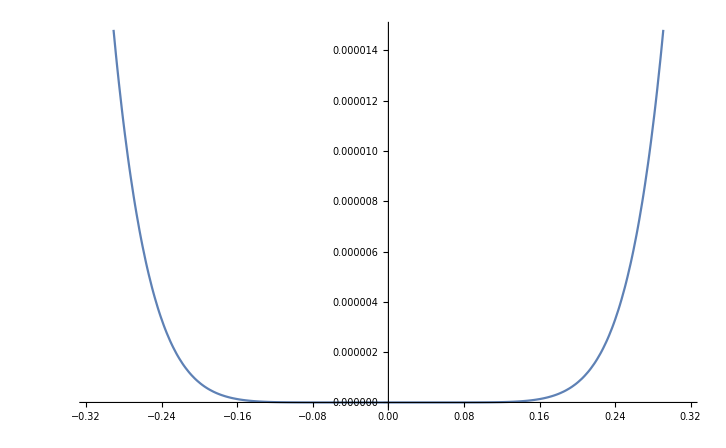

{-2,-1,0,1,2,3,4}

{0,{kx→0}}

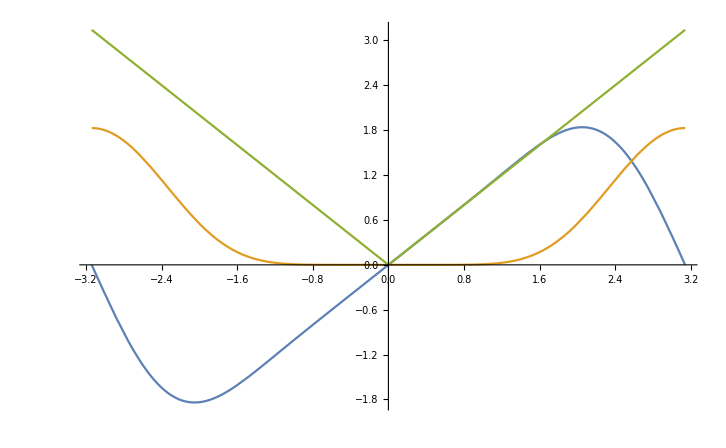

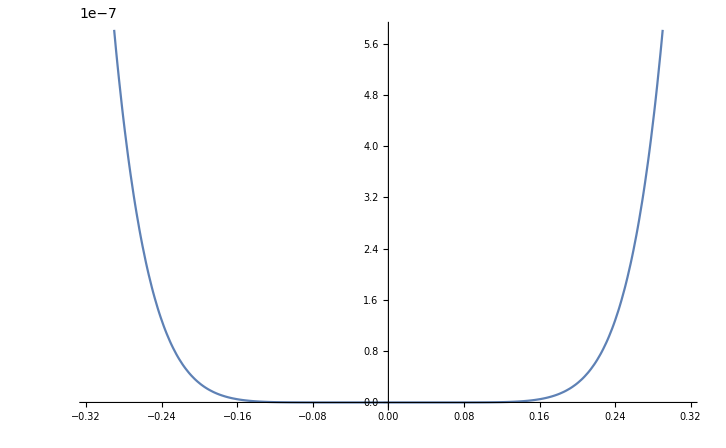

{-2,-1,0,1,2,3,4}

{0,{kx→0}}

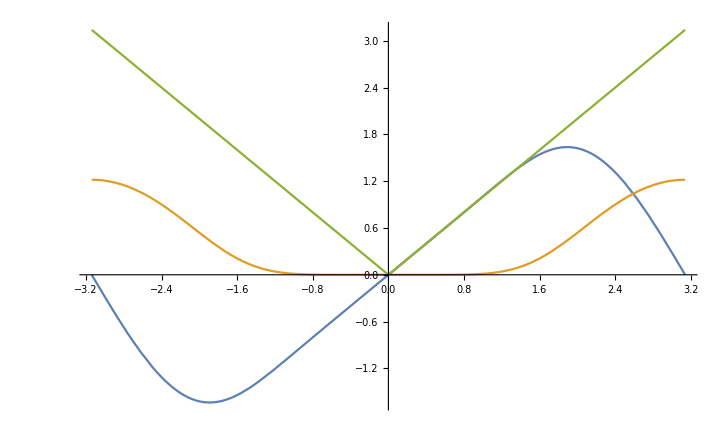

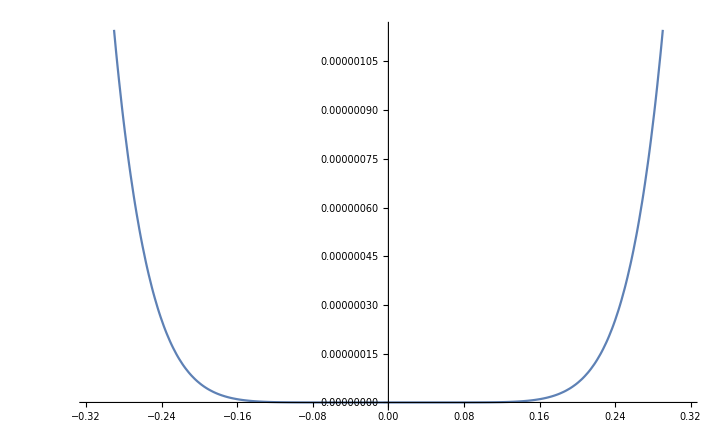

{-3,-1,0,1,2,3,4}

{0,{kx→0}}

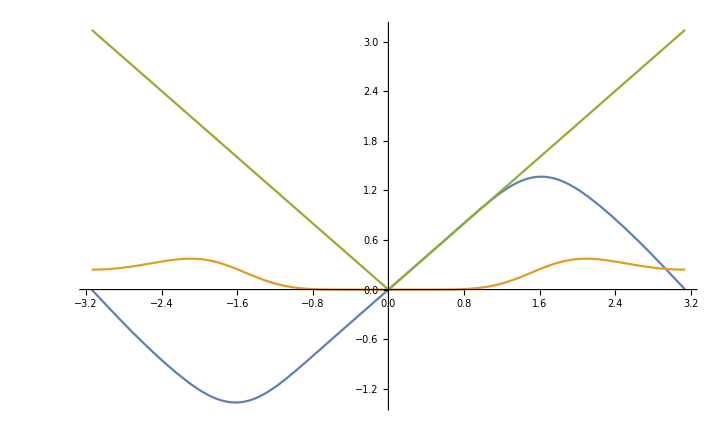

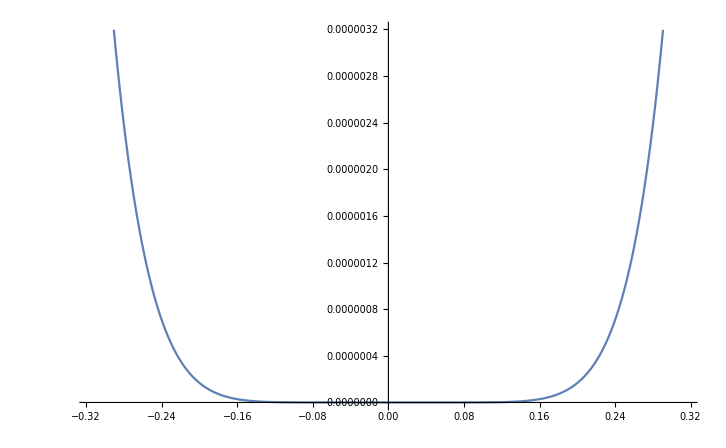

{-4,-2,0,1,2,3,4}

{1/2520(-252 Cos[4]+2048 Cos[2] Cos[4]-1155 Cos[4]^2-840 Cos[4] Cos[8]+252 Cos[4] Cos[12]-60 Cos[4] Cos[16]+7 Cos[4] Cos[20]+2048 Sin[2] Sin[4]-1155 Sin[4]^2-840 Sin[4] Sin[8]+252 Sin[4] Sin[12]-60 Sin[4] Sin[16]+7 Sin[4] Sin[20]),{kx→-2}}

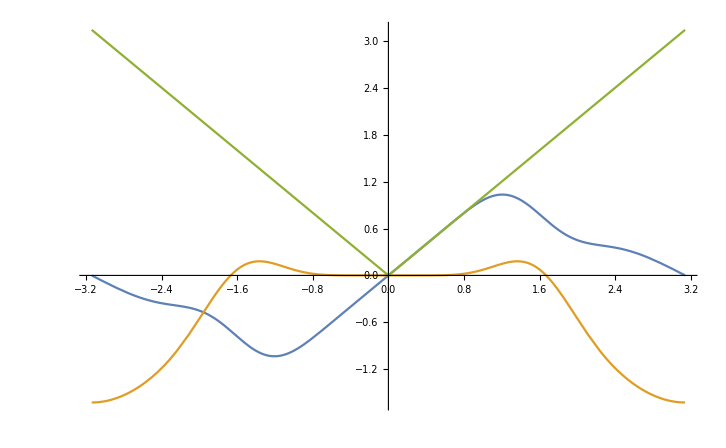

-Graphics-

{-4,-2,0,2,3,4,5}

{0,{kx→0}}

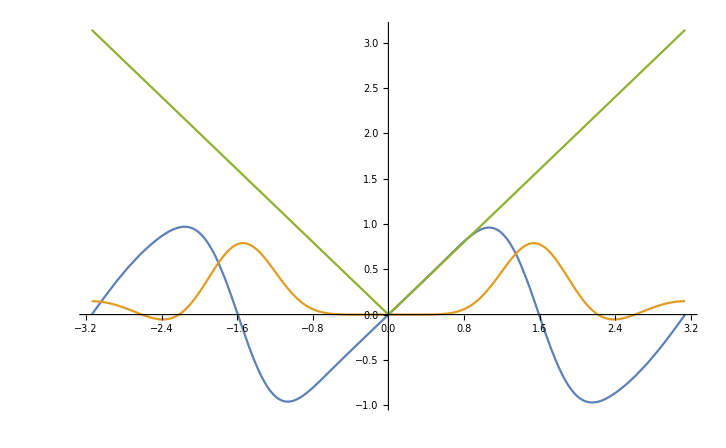

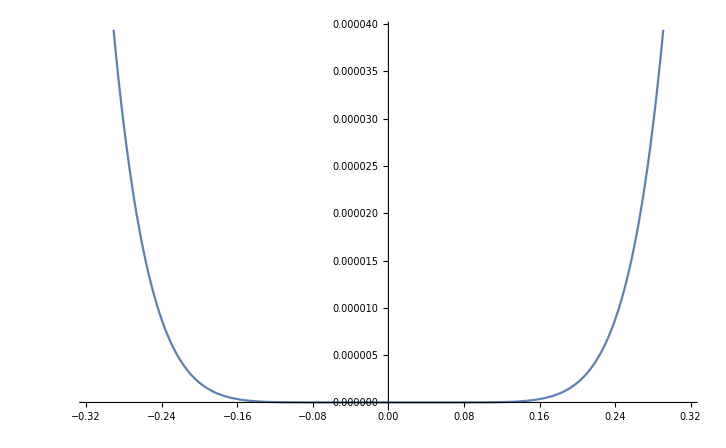

{-4,-2,0,2,4,5,6}

{0,{kx→0}}

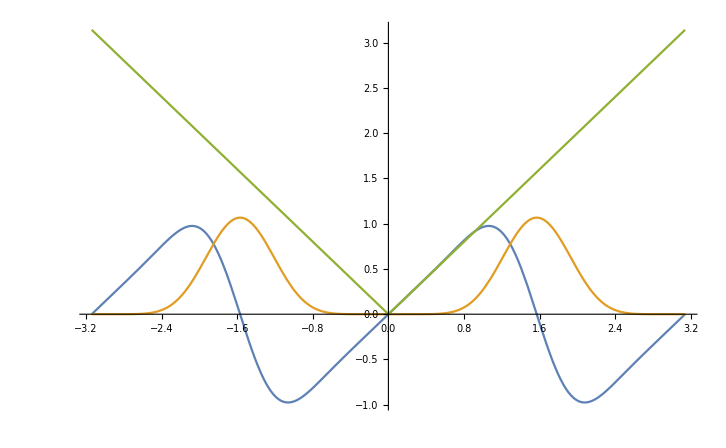

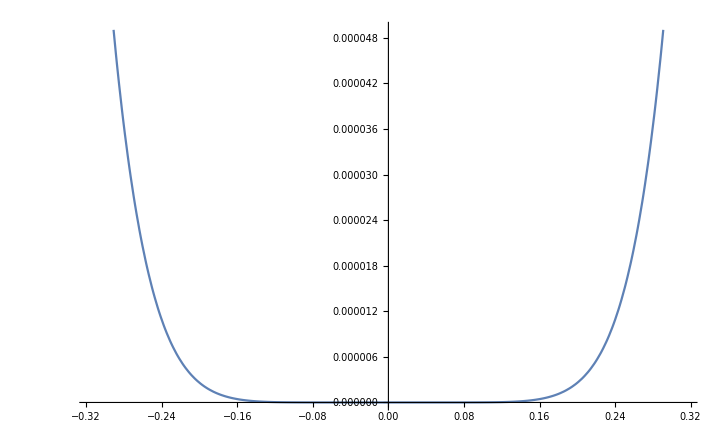

{-4,-2,0,2,4,6,7}

{0,{kx→0}}

-Graphics-

-Graphics-

```mathematica
idx =3;
Δ=1;
tempOut[kx_] =  ω[kx]/.Sol[kx][[4]][[idx]]
Plot[Im[tempOut[kx]],{kx,-π/10,π/10}]
For [i=1,i<=Length[pointsM],i++,
tempGrid[kx_] = ω[kx]/.Sol[kx][[i]][[idx]];

If[idx<3,pointsP[[i]]//Print;,pointsM[[i]]//Print;];
If[idx<3,
Minimize[{ComplexExpand[Im[tempGrid[kx]]],0<=kx<=2},{kx}] // Print;,
Minimize[{ComplexExpand[Im[tempGrid[kx]]],-2<=kx<=0},{kx}]// Print;];

Plot[{Re[tempGrid[kx]],Im[tempGrid[kx]],Norm[kx]},{kx,-π/1,π/1}]//Print;
Plot[Im[tempGrid[kx]],{kx,-π/10,π/10}]//Print;
]
```